```mathematica
NDSolve[{.01 y''[x]-(1+3x^2)y[x]-x==0,y[0]==1,y[1]==1},y[x],{x,0,1}]
```

{{y[x]→InterpolatingFunction[{{0., 1.}}, <>][x]}}

```mathematica
%2[[1,1,2]]
```

InterpolatingFunction[{{0., 1.}}, <>][x]

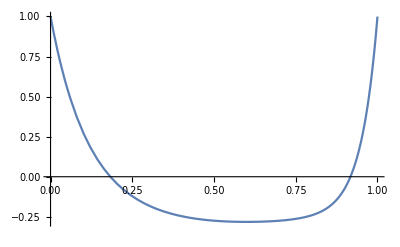

```mathematica
Plot[%3,{x,0,1}]
```

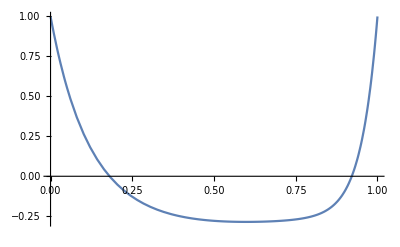

```mathematica
Plot[-x/(1+3x^2)+Exp[-x/Sqrt[.01]]+5/4Exp[2(x-1)/Sqrt[.01]],{x,0,1}]
```